## Fig. S5B

Generate plot showing how R_σ depends on strategy, for comparison to critical budget changes.

```mathematica
Clear["Global'*"];
SetDirectory[NotebookDirectory[]];
```

```mathematica
s1=0.4;
s2=1-s1;
```

```mathematica
f[x_,e_]:=s1/(e*x)+s2/(e(1-x));
```

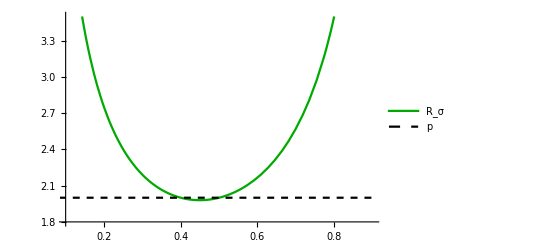

```mathematica
Plot[{f[x,1],2},{x,.01,.9},PlotRange->{{.1,.9},{1.8,3.5}},TicksStyle->Directive[Black, 12],PlotLegends->{"R_σ","p"},PlotStyle->{Green//Darker,Directive[Black,Dashed]}]
```

```mathematica
Export["figS5B.svg",%];
```